# Toolbox Cheat Sheet

```mathematica
<<MASSToolbox`
<<MASSToolbox`Style`
```

## Most important Toolbox functions and data structures

```mathematica
model=ExampleData[{"MASSToolbox","Glycolysis"}];
```

### stripUnits

```mathematica
model["InitialConditions"]
stripUnits[model["InitialConditions"]]
```

{glu^c→1. Millimole Liter^-1,g6p^c→0.0486 Millimole Liter^-1,f6p^c→0.0198 Millimole Liter^-1,fdp^c→0.0146 Millimole Liter^-1,dhap^c→0.16 Millimole Liter^-1,gap^c→0.00728 Millimole Liter^-1,pg13^c→0.000243 Millimole Liter^-1,pg3^c→0.0773 Millimole Liter^-1,pg2^c→0.0113 Millimole Liter^-1,pep^c→0.017 Millimole Liter^-1,pyr^c→0.060301 Millimole Liter^-1,lac^c→1.36 Millimole Liter^-1,nad^c→0.0589 Millimole Liter^-1,nadh^c→0.0301 Millimole Liter^-1,amp^c→0.0867281 Millimole Liter^-1,adp^c→0.29 Millimole Liter^-1,atp^c→1.6 Millimole Liter^-1,phos^c→2.5 Millimole Liter^-1,h^c→0.0000899757 Millimole Liter^-1,h2o^c→1. Millimole Liter^-1,v_vhk→1.12 Millimole Hour^-1 Liter^-1,v_vpgi→1.12 Millimole Hour^-1 Liter^-1,v_vpfk→1.12 Millimole Hour^-1 Liter^-1,v_vtpi→1.12 Millimole Hour^-1 Liter^-1,v_vald→1.12 Millimole Hour^-1 Liter^-1,v_vgapdh→2.24 Millimole Hour^-1 Liter^-1,v_vpgk→2.24 Millimole Hour^-1 Liter^-1,v_vpglm→2.24 Millimole Hour^-1 Liter^-1,v_veno→2.24 Millimole Hour^-1 Liter^-1,v_vpk→2.24 Millimole Hour^-1 Liter^-1,v_vldh→2.016 Millimole Hour^-1 Liter^-1,v_vamp→0.014 Millimole Hour^-1 Liter^-1,v_vapk→0. Millimole Hour^-1 Liter^-1,v_vpyr→0.224 Millimole Hour^-1 Liter^-1,v_vlac→2.016 Millimole Hour^-1 Liter^-1,v_vatp→2.24 Millimole Hour^-1 Liter^-1,v_vnadh→0.224 Millimole Hour^-1 Liter^-1,v_vgluin→1.12 Millimole Hour^-1 Liter^-1,v_vampin→0.014 Millimole Hour^-1 Liter^-1,v_vh→2.688 Millimole Hour^-1 Liter^-1,v_vh2o→0. Millimole Hour^-1 Liter^-1}

{glu^c→1.,g6p^c→0.0486,f6p^c→0.0198,fdp^c→0.0146,dhap^c→0.16,gap^c→0.00728,pg13^c→0.000243,pg3^c→0.0773,pg2^c→0.0113,pep^c→0.017,pyr^c→0.060301,lac^c→1.36,nad^c→0.0589,nadh^c→0.0301,amp^c→0.0867281,adp^c→0.29,atp^c→1.6,phos^c→2.5,h^c→0.0000899757,h2o^c→1.,v_vhk→1.12,v_vpgi→1.12,v_vpfk→1.12,v_vtpi→1.12,v_vald→1.12,v_vgapdh→2.24,v_vpgk→2.24,v_vpglm→2.24,v_veno→2.24,v_vpk→2.24,v_vldh→2.016,v_vamp→0.014,v_vapk→0.,v_vpyr→0.224,v_vlac→2.016,v_vatp→2.24,v_vnadh→0.224,v_vgluin→1.12,v_vampin→0.014,v_vh→2.688,v_vh2o→0.}

### stripTime

```mathematica
model["Rates"]
stripTime@model["Rates"]
```

{Volume_c k_vhk^⟶ (-(adp^c[t] g6p^c[t])/K_vhk+atp^c[t] glu^c[t]),Volume_c k_vpgi^⟶ (-f6p^c[t]/K_vpgi+g6p^c[t]),Volume_c k_vpfk^⟶ (atp^c[t] f6p^c[t]-(adp^c[t] fdp^c[t])/K_vpfk),Volume_c k_vtpi^⟶ (dhap^c[t]-gap^c[t]/K_vtpi),Volume_c k_vald^⟶ (fdp^c[t]-(dhap^c[t] gap^c[t])/K_vald),Volume_c k_vgapdh^⟶ (-(nadh^c[t] pg13^c[t])/K_vgapdh+gap^c[t] nad^c[t] phos^c[t]),Volume_c k_vpgk^⟶ (adp^c[t] pg13^c[t]-(atp^c[t] pg3^c[t])/K_vpgk),Volume_c k_vpglm^⟶ (-pg2^c[t]/K_vpglm+pg3^c[t]),Volume_c k_veno^⟶ (-pep^c[t]/K_veno+pg2^c[t]),Volume_c k_vpk^⟶ (adp^c[t] pep^c[t]-(atp^c[t] pyr^c[t])/K_vpk),Volume_c k_vldh^⟶ (-(lac^c[t] nad^c[t])/K_vldh+nadh^c[t] pyr^c[t]),Volume_c k_vamp^⟶ (-amp^Xt/K_vamp+amp^c[t]),Volume_c k_vapk^⟶ ((adp^c[t])^2-(amp^c[t] atp^c[t])/K_vapk),Volume_c k_vpyr^⟶ (-pyr^Xt/K_vpyr+pyr^c[t]),Volume_c k_vlac^⟶ (-lac^Xt/K_vlac+lac^c[t]),Volume_c k_vatp^⟶ (atp^c[t]-(adp^c[t] phos^c[t])/K_vatp),Volume_c k_vnadh^⟶ (-nad^c[t]/K_vnadh+nadh^c[t]),Volume_c k_vgluin^⟶ (glu^Xt-glu^c[t]/K_vgluin),Volume_c k_vampin^⟶ (amp^Xt-amp^c[t]/K_vampin),Volume_c k_vh^⟶ (-h^Xt/K_vh+h^c[t]),Volume_c k_vh2o^⟶ (-h2o^Xt/K_vh2o+h2o^c[t])}

{(-(adp^c g6p^c)/K_vhk+atp^c glu^c) Volume_c k_vhk^⟶,(-f6p^c/K_vpgi+g6p^c) Volume_c k_vpgi^⟶,(atp^c f6p^c-(adp^c fdp^c)/K_vpfk) Volume_c k_vpfk^⟶,(dhap^c-gap^c/K_vtpi) Volume_c k_vtpi^⟶,(fdp^c-(dhap^c gap^c)/K_vald) Volume_c k_vald^⟶,(-(nadh^c pg13^c)/K_vgapdh+gap^c nad^c phos^c) Volume_c k_vgapdh^⟶,(adp^c pg13^c-(atp^c pg3^c)/K_vpgk) Volume_c k_vpgk^⟶,(-pg2^c/K_vpglm+pg3^c) Volume_c k_vpglm^⟶,(-pep^c/K_veno+pg2^c) Volume_c k_veno^⟶,(adp^c pep^c-(atp^c pyr^c)/K_vpk) Volume_c k_vpk^⟶,(-(lac^c nad^c)/K_vldh+nadh^c pyr^c) Volume_c k_vldh^⟶,(amp^c-amp^Xt/K_vamp) Volume_c k_vamp^⟶,((adp^c)^2-(amp^c atp^c)/K_vapk) Volume_c k_vapk^⟶,(pyr^c-pyr^Xt/K_vpyr) Volume_c k_vpyr^⟶,(lac^c-lac^Xt/K_vlac) Volume_c k_vlac^⟶,(atp^c-(adp^c phos^c)/K_vatp) Volume_c k_vatp^⟶,(-nad^c/K_vnadh+nadh^c) Volume_c k_vnadh^⟶,(-glu^c/K_vgluin+glu^Xt) Volume_c k_vgluin^⟶,(-amp^c/K_vampin+amp^Xt) Volume_c k_vampin^⟶,(h^c-h^Xt/K_vh) Volume_c k_vh^⟶,(h2o^c-h2o^Xt/K_vh2o) Volume_c k_vh2o^⟶}

### constructModel

### Quick fixes

```mathematica
model=ExampleData[{"MASSToolbox","Glycolysis"}];
```

```mathematica
concSol=simulate[model][[1]];
```

NDSolve::mxst: Maximum number of 10000 steps reached at the point t == 1.37062×10^12.

```mathematica
NullSpace[modelᵀ].model["Species"]
```

{adp^c+2 atp^c+dhap^c+f6p^c+2 fdp^c+g6p^c+gap^c+pep^c+2 pg13^c+pg2^c+pg3^c+phos^c,nad^c+nadh^c}

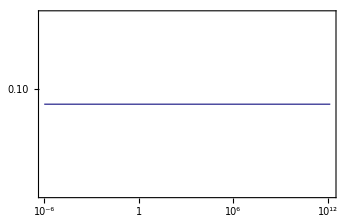

```mathematica
plotSimulation[{"pool"->nad^c+nadh^c}/.concSol]
```